# Walk Effect of Trigger Plastics

```mathematica
(* physics of scattered protons *)
(* geometry of trigger plastics *)
(* ligth signal propagating and attenuated along the plastics *)
(* Result *)
```

```mathematica
Remove[t1,t2]
```

## General

```mathematica
βplastic=1/1.5;
c=299.792458;
x1=200;
x2=-1000;
Q1[Q_,x_,att_]:=Q Exp[-Abs[x1-x]/att]
Q2[Q_,x_,att_]:=Q Exp[-Abs[x-x2]/att]
W[Q_,Qth_]:=(40Log[Q/(Q-Qth)])^(1/3)
t1[x_]:=Abs[x-x1]/(βplastic c)
t2[x_]:=Abs[x2-x]/(βplastic c)
```

```mathematica
Manipulate[Plot[-Q(1-Exp[-t^3/40]),{t,0,6},PlotRange->{-1,0},AspectRatio->2],{Q,0,1}]
```

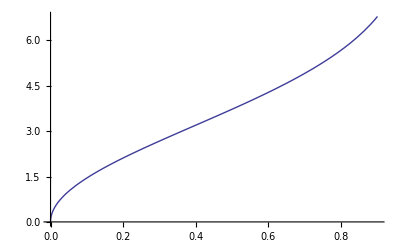

```mathematica
Plot[W[1,α],{α,0,0.9},PlotRange->{0,All}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x,W[Q1[Q,x,2180],Qth]-W[Q2[Q,x,2180],Qth]}
},{Q,1,8},{x,-1000,200},PlotRange->All,AspectRatio->1]
,{Qth,0.1,1}]
```

```mathematica
Manipulate[ParametricPlot[{
{Q1[Q,x,att],Q2[Q,x,att]}
},{x, -1000, 200},{Q,0,50},
GridLines->Automatic,GridLinesStyle->Directive[Dashed],PlotRange->{{0,50},{0, 50}},AspectRatio->1],
{att,2000,5000}]
```

```mathematica
Manipulate[ParametricPlot[{

{t1[x]-t2[x]+W[Q1[Q,x,att],Qth]-W[Q2[Q,x,att],Qth],Log[Q1[Q,x,att]/Q2[Q,x,att]]}

},{x, -1000, 200},{Q,1,8},PlotRange->{{-10,10},{-1,1}},AspectRatio->1,
GridLines->Automatic,GridLinesStyle->Directive[Dashed],PlotRange->All,
Epilog->Text[TableForm[{(βplastic c)/att,(βplastic c)/att 5}],{5, 0.5}]],
{{att,2180},2000,5000},{{Qth,0.9},0.1,0.9}]
```

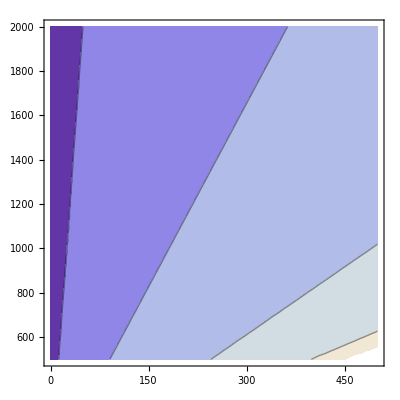

```mathematica
ContourPlot[W[Q,Qth],{Qth,0,500},{Q,500,2000}]
```

```mathematica
Manipulate[ParametricPlot[{

{x,W[Q1[Q,x,att],Qth]-W[Q2[Q,x,att],Qth]}

},{x, -1000, 200},{Q,500,2000},AspectRatio->1,PlotRange->{{-1000,200},{-6,6}},
GridLines->Automatic,GridLinesStyle->Directive[Dashed],PlotRange->All],
{{att,2180},2000,5000},{{Qth,500},0,500}]
```

## PP elastics

```mathematica
(* physics *)
mp=938.27203;
c=299.792458; (* mm/ns *)
Tinc=260;
P[θNN_,ϕNN_,id_]:={mp+Tinc If[id==1,Cos[θNN/2]^2,Sin[θNN/2]^2],-(-1)^id(√(mp Tinc) Cos[ϕNN] Sin[θNN])/(√2),-(-1)^id(√(mp Tinc) Sin[θNN] Sin[ϕNN])/(√2),√(Tinc (2 mp+Tinc)) If[id==1,Cos[θNN/2]^2,Sin[θNN/2]^2]}
```

```mathematica
(* Observable *)
KE[A_]:=A[[1]]-mp
Mom[A_]:=Norm[A[[2;;4]]]
θ[A_]:=If[A[[2;;3]]=={0,0},0,ArcTan[A[[4]],Norm[A[[2;;3]]]]]
ϕ[A_]:=If[A[[2;;3]]=={0,0},0,ArcTan[A[[2]],A[[3]]]]
α[A_]:=A[[1]]/mp
β[α_]:=√(1-1/α^2)
```

```mathematica
Manipulate[ParametricPlot[{(1/(√(1-(1000/((t+k) c))^2))-1),(1/(√(1-(1000/(t c))^2))-1)},{t,5, 30}],{k,0,3}]
```

```mathematica
(* geometry *)
d=1400; (* mm *)
θp={π/3,-π/3};
fl[A_,plasticID_]:= d/(Cos[ϕ[A]]Sin[θ[A]]Sin[θp[[plasticID]]]+Cos[θ[A]]Cos[θp[[plasticID]]])
ToF[A_,plasticID_]:= fl[A,plasticID]/(β[α[A]]c) (*ns *)
HitPoint[A_,plasticID_]:=fl[A,plasticID]Normalize[A[[2;;4]]]
Obser[A_,id_]:=TableForm[{
A,
{KE[A],Mom[A]},
{θ[A],ϕ[A]}180/π,
{α[A],β[α[A]]},
{fl[A,id],ToF[A,id]},
HitPoint[A,id]
}]
```

```mathematica
Manipulate[Obser[P[θNN °,ϕNN °,1],1],{θNN,0,140},{{ϕNN,0},-20, 20}]
```

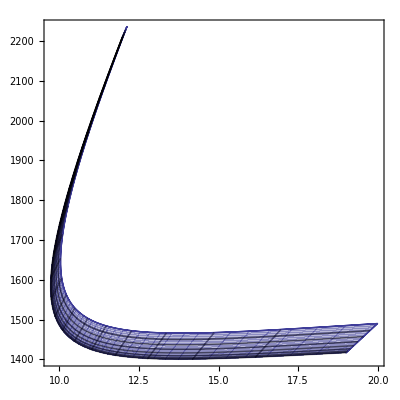

```mathematica
ParametricPlot[
{ToF[P[θNN °,ϕNN °,1],1],fl[P[θNN °,ϕNN °,1],1]}
,{θNN,20,140},{ϕNN,-20, 20},AspectRatio->1]
```

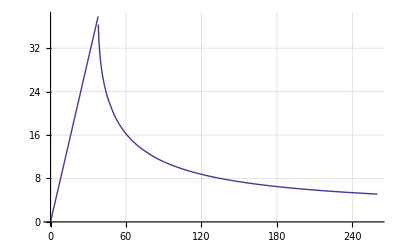

```mathematica
(* energy deposite for 13mm plastics H10C9*)
EngLostList={
{37.9246,37.9246},
{37.93,37.67},
{37.95,37.158},
{38,36.434},
{38.1,35.497},
{38.3,34.231},
{38.5,33.292},
{39,31.555},
{39.5,30.251},
{40,29.185},
{41,27.481},
{42,26.133},
{45,23.196},
{50,20.034},
{55,17.864},
{60,16.24},
{70,13.915},
{80,12.294},
{100,10.148},
{120,8.7662},
{140,7.7921},
{160,7.0674},
{180,6.5046},
{200,6.0549},
{220,5.688},
{225.9,5.5924},
{240,5.3815},
{250,5.2467},
{260,5.1223}};
LightOutput[x_]:=Piecewise[{{x,0≤ x<37.9246},{Interpolation[EngLostList,x],37.9246≤ x<260}}]
Plot[LightOutput[x],{x,0,260},PlotRange->{{0,260},{0,All}},GridLines->Automatic,GridLinesStyle->Directive[Dashed]]
```

```mathematica
(* Plastics Signal *)
βplastic=1/1.58;
att={4000,2500}; (* mm *)
```

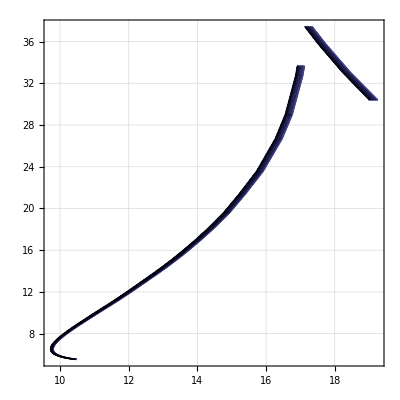

```mathematica
ParametricPlot[
{ToF[P[θNN °,ϕNN °,1],1],LightOutput[KE[P[θNN °,ϕNN °,1]]]},{θNN,40, 140},{ϕNN,-10, 10},AspectRatio->1,PlotRange->{0,All},GridLines->Automatic,GridLinesStyle->Directive[Dashed]]
```

## Signal

```mathematica
(* length to the PMT *)
(* PMT position *)
PosF[id_]:=d {Sin[θp[[id]]],0,Cos[θp[[id]]]}+d Tan[θp[[id]]+(-1)^id 20 °]{-Sin[π/2-θp[[id]]],0,Cos[π/2-θp[[id]]]}//N
PosB[id_]:=d {Sin[θp[[id]]],0,Cos[θp[[id]]]}+d Tan[θp[[id]]+(-1)^id 70 °]{-Sin[π/2-θp[[id]]],0,Cos[π/2-θp[[id]]]}//N
Norm[PosB[1]-PosF[1]]
ArcCos[Normalize[PosF[1]].{0,0,1}] 180/π
ArcCos[Normalize[PosB[1]].Normalize[PosF[1]]] 180/π
```

1421.6

20.

50.

```mathematica
Remove[tF,tB,ΓF,ΓB,QB,QF,Qsum,Qlog,Tavg,ΔT]
```

```mathematica
(* Signal *)
QB[θNN_,ϕNN_,id_]:=LightOutput[KE[P[θNN,ϕNN,id]]]Exp[-Norm[HitPoint[P[θNN,ϕNN,id],id]-PosB[id]]/att[[id]]]
QF[θNN_,ϕNN_,id_]:=LightOutput[KE[P[θNN,ϕNN,id]]]Exp[-Norm[HitPoint[P[θNN,ϕNN,id],id]-PosF[id]]/att[[id]]]
ΓB[θNN_,ϕNN_,id_]:=Norm[HitPoint[P[θNN,ϕNN,id],id]-PosB[id]]/(βplastic c)+ToF[P[θNN,ϕNN,id],id]
ΓF[θNN_,ϕNN_,id_]:=Norm[HitPoint[P[θNN,ϕNN,id],id]-PosF[id]]/(βplastic c)+ToF[P[θNN,ϕNN,id],id]
tB[θNN_,ϕNN_,id_]:=ΓB[θNN,ϕNN,id]-ΓF[θNN,ϕNN,1]
tF[θNN_,ϕNN_,id_]:=ΓF[θNN,ϕNN,id]-ΓF[θNN,ϕNN,1]
```

```mathematica
Qsum[θNN_,ϕNN_,id_]:=√(QB[θNN,ϕNN,id]QF[θNN,ϕNN,id])
Qlog[θNN_,ϕNN_,id_]:=Log[QB[θNN,ϕNN,id]/QF[θNN,ϕNN,id]]
Tavg[θNN_,ϕNN_,id_]:=1/2(tB[θNN,ϕNN,id]+tF[θNN,ϕNN,id])
ΔT[θNN_,ϕNN_,id_]:=tB[θNN,ϕNN,id]-tF[θNN,ϕNN,id]
```

```mathematica
ObserAll[θNN_,ϕNN_,id_]:=TableForm[{
P[θNN,ϕNN,id],
{"KE and Mom",KE[P[θNN,ϕNN,id]],Mom[P[θNN,ϕNN,id]]},
{"Polar Angle",θ[P[θNN,ϕNN,id]] 180/π,ϕ[P[θNN,ϕNN,id]] 180/π},
{"α  and  β",α[P[θNN,ϕNN,id]],β[α[P[θNN,ϕNN,id]]]},
{"fl and ToF",fl[P[θNN,ϕNN,id],id],ToF[P[θNN,ϕNN,id],id]},
HitPoint[P[θNN,ϕNN,id],id],
{"Light Output",LightOutput[KE[P[θNN,ϕNN,id]]], "atten length",att[[id]]},
{"Distance to PMT",Norm[HitPoint[P[θNN,ϕNN,id],id]-PosB[id]],Norm[HitPoint[P[θNN,ϕNN,id],id]-PosF[id]]},
{"QB and ΓB",QB[θNN,ϕNN,id],ΓB[θNN,ϕNN,id]},
{"QF and ΓF",QF[θNN,ϕNN,id],ΓF[θNN,ϕNN,id]},
{"Qsum","Qlog","Tavg","ΔT"},
{Qsum[θNN,ϕNN,id],Qlog[θNN,ϕNN,id],Tavg[θNN,ϕNN,id],ΔT[θNN,ϕNN,id]}
}]
```

```mathematica
Manipulate[
TableForm[{
{"Polar Angle",θ[P[θNN,ϕNN,1]] 180/π,ϕ[P[θNN,ϕNN,1]] 180/π,"|",θ[P[θNN,ϕNN,2]] 180/π,ϕ[P[θNN,ϕNN,2]] 180/π},
{"fl and ToF",fl[P[θNN,ϕNN,1],1],ToF[P[θNN,ϕNN,1],1],"|",fl[P[θNN,ϕNN,2],2],ToF[P[θNN,ϕNN,2],2]},
{"QB and ΓB",QB[θNN,ϕNN,1],ΓB[θNN,ϕNN,1],"|",QB[θNN,ϕNN,2],ΓB[θNN,ϕNN,2]},
{"QB and ΓB",QF[θNN,ϕNN,1],ΓF[θNN,ϕNN,1],"|",QF[θNN,ϕNN,2],ΓF[θNN,ϕNN,2]},
{"","Tavg(1)","ΔT(1)","|","Tavg(2)","ΔT(2)"},
{"",Tavg[θNN,ϕNN,1],ΔT[θNN,ϕNN,1],"|",Tavg[θNN,ϕNN,2],ΔT[θNN,ϕNN,2]}
}]
,{θNN,40°,140 °},{{ϕNN,0},-20 °, 20 °}]
```

```mathematica
Manipulate[
Show[
Graphics3D[{
Arrow[{{0,0,0},{0,0,1500}}],
Arrow[{{0,0,0},{1000,0,0}}],
Arrow[{{0,0,0},{0,200,0}}],
Red,Line[{{0,0,0},HitPoint[P[θNN °,ϕNN °,1],1]}],
Blue,Line[{{0,0,0},HitPoint[P[θNN °,ϕNN °,2],2]}],
Black,PointSize[Large],Point[{PosF[1],PosB[1],PosF[2],PosB[2]}],
Orange, Line[{PosF[1],HitPoint[P[θNN °,ϕNN °,1],1],PosB[1]}]
}],
ParametricPlot3D[{HitPoint[P[a °,b °,1],1],HitPoint[P[a °,b °,2],2]},{a,50,140},{b,-20,20}]
]
,{θNN,40,140},{{ϕNN,0},-20, 20}]
```

```mathematica
Manipulate[ObserAll[θNN °,ϕNN °,id],{θNN,40,140},{{ϕNN,0},-20, 20},{att,2000,50000},{id,{1,2}}]
```

```mathematica
ParametricPlot3D[{θ[P[θNN,0,1]] 180/π,KE[P[θNN ,0,1]],LightOutput[KE[P[θNN ,0,1]]]},{θNN,20 °, 160 °},AspectRatio->0.7,AxesLabel->{"Lab θ","KE","LightOutput"},BoxRatios->1]
```

-Graphics3D-

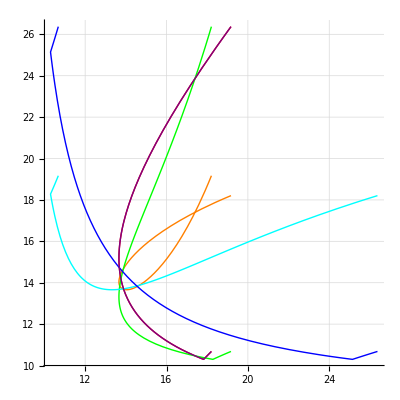

```mathematica
ParametricPlot[
{
{ΓB[θNN °,0,1],ΓF[θNN °,0,1]},
{ΓB[θNN °,0,1],ΓB[θNN °,0,2]},
{ΓB[θNN °,0,1],ΓF[θNN °,0,2]},
{ΓF[θNN °,0,1],ΓB[θNN °,0,2]},
{ΓF[θNN °,0,1],ΓF[θNN °,0,2]},
{ΓB[θNN °,0,2],ΓF[θNN °,0,2]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Orange,Green, Cyan, Blue, Purple}]
```

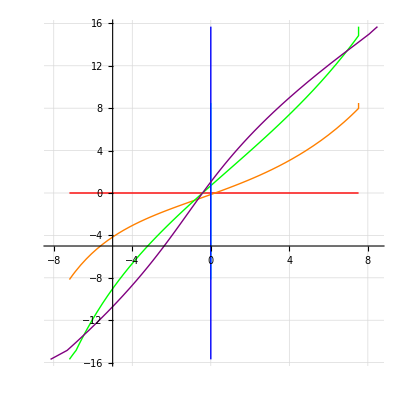

```mathematica
ParametricPlot[
{
{tB[θNN °,0,1],tF[θNN °,0,1]},
{tB[θNN °,0,1],tB[θNN °,0,2]},
{tB[θNN °,0,1],tF[θNN °,0,2]},
{tF[θNN °,0,1],tB[θNN °,0,2]},
{tF[θNN °,0,1],tF[θNN °,0,2]},
{tB[θNN °,0,2],tF[θNN °,0,2]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Orange,Green, Cyan, Blue, Purple},AxesOrigin->{-5,-5}]
```

```mathematica
Manipulate[ParametricPlot[
{
{θ[P[θNN °,0,id]] 180/π,QB[θNN °,0,id]/Qsum[θNN °,0,id]},
{θ[P[θNN °,0,id]] 180/π,QF[θNN °,0,id]/Qsum[θNN °,0,id]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue}],
{id,{1,2}}]
```

```mathematica
Manipulate[Plot[Exp[(1500-2x)/(2 a)],{x,0,1500},GridLines->Automatic,GridLinesStyle->Directive[Dashed],PlotRange->{0.5,1.5}],{a,2000,4000}]
```

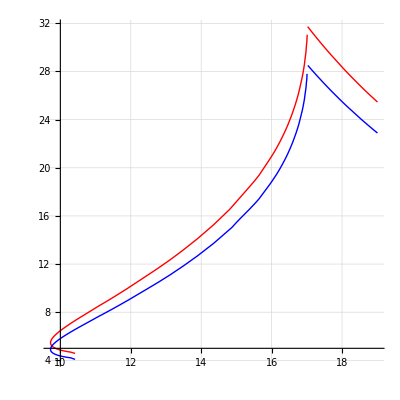

```mathematica
ParametricPlot[
{
{ToF[P[θNN °,0,1],1],Qsum[θNN °,0,1]},
{ToF[P[θNN °,0,2],2],Qsum[θNN °,0,2]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue}]
```

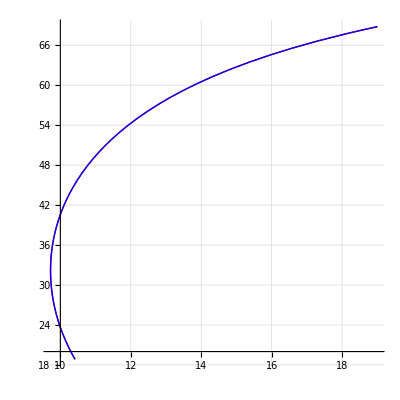

```mathematica
ParametricPlot[
{
{ToF[P[θNN °,0,1],1],θ[P[θNN °,0,1]] 180/π},
{ToF[P[θNN °,0,2],2],θ[P[θNN °,0,2]] 180/π}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue}]
```

```mathematica
Manipulate[ParametricPlot[
{
{θ[P[θNN °,0,id]] 180/π,ΔT[θNN °,0,id]},
{θ[P[θNN °,0,id]] 180/π,Tavg[θNN °,0,id]}
},
{θNN,40,140},PlotRange->{{20,70},All},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->0.6,PlotStyle->{Red,Blue}]
,{id,{1,2}}]
```

```mathematica
Manipulate[ParametricPlot[
{
(* Red  *){ΓF[θNN °,0,id]-1500/(βplastic c),QF[θNN °,0,id]},
(* Blue *){ΓB[θNN °,0,id]-1500/(βplastic c),QB[θNN °,0,id]},
(*Orange*){(ΓB[θNN °,0,id]+ΓF[θNN °,0,id])/2-1500/(2βplastic c),Qsum[θNN °,0,id]},
(*Green *){ΓB[θNN °,0,id]-ΓF[θNN °,0,id],Qsum[θNN °,0,id]},
},
{θNN,40,140},PlotRange->{{-10,20},{0,40}},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue,Orange,Green,Black},AxesOrigin->{-10,0}]
,{id,{1,2}}]
```

```mathematica
Manipulate[ParametricPlot[
{
(*Black *){ΓF[θNN °,0 ,1],QF[θNN °,0,1]},
(* Red  *){ΓF[θNN °,0,id],QF[θNN °,0,id]},
(* Blue *){ΓB[θNN °,0,id],QB[θNN °,0,id]},
(* Pink *){tF[θNN °,0,id],QF[θNN °,0,id]},
(* Cyan *){tB[θNN °,0,id],QB[θNN °,0,id]},
(*Orange*){ΔT[θNN °,0,id],Qsum[θNN °,0,id]},
(*Green *){Tavg[θNN °,0,id],Qsum[θNN °,0,id]}
},
{θNN,40,140},PlotRange->{{-20,30},{0,40}},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Black,Red,Blue,Pink, Cyan,Orange,Green},AxesOrigin->{-20,0},
Epilog->{
Pink,Text["tF",{tF[40 °,0,id],QF[40 °,0,id]}],
Cyan,Text["tB",{tB[40 °,0,id],QB[40 °,0,id]}],
Green,Text["Tavg",{Tavg[40 °,0,id],Qsum[40 °,0,id]}],
Orange,Text["ΔT",{ΔT[40 °,0,id],Qsum[40 °,0,id]}]
}]
,{{id,2},{1,2}}]
```

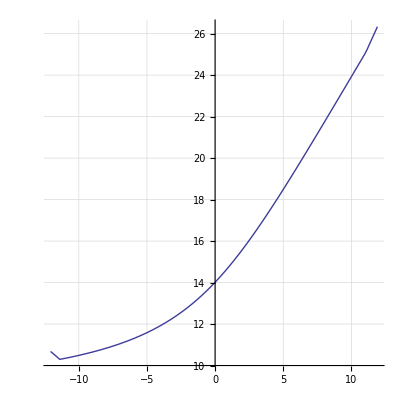

```mathematica
ParametricPlot[
{
{-Tavg[θNN °,0,2],ΓF[θNN °,0,1]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1]
```

```mathematica
Manipulate[ParametricPlot[
{{Qsum[θNN °,0,1],Qsum[θNN °,0,2]},
{QB[θNN °,0,id],QF[θNN °,0,id]}
},
{θNN,40,140},PlotRange->{{0,35},{0,35}},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue,Green},AxesOrigin->{0,0},
Epilog->Text["Slope="<>ToString[(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])],{25,25}]]
,{id,{1,2}},{att,2000,5000},{{p1,{10,10}},Locator},{{p2,{20,10}},Locator}]
```

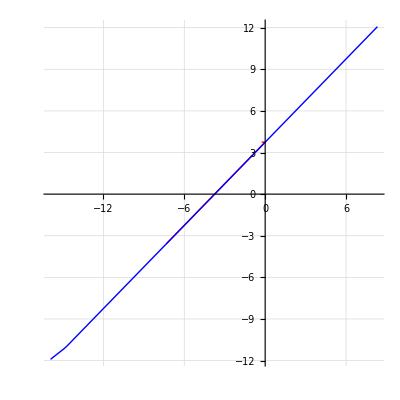

```mathematica
ParametricPlot[
{
{ToF[P[θNN °,0,1],1]-ΓF[θNN °,0,1],Tavg[θNN °,0,1]},
{ToF[P[θNN °,0,2],2]-ΓF[θNN °,0,1],Tavg[θNN °,0,2]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue}]
```

```mathematica
Manipulate[ParametricPlot[
{
{tB[θNN °,0,id],tF[θNN °,0,id]},
{Tavg[θNN °,0,id],ΔT[θNN °,0,id]}
},
{θNN,40,140},PlotRange->{{-15,15},{-20,20}},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue},AxesOrigin->{-15,-20}]
,{id,{1,2}}]
```

```mathematica
Manipulate[ParametricPlot[
{
{ΔT[θNN °,0,id],Qlog[θNN °,0,id]},
{Tavg[θNN °,0,id],Qlog[θNN °,0,id]}
},
{θNN,40,140},PlotRange->{{-15,15},{-1,1}},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue},AxesOrigin->{-15,-1}]
,{id,{1,2}}]
```

```mathematica
Manipulate[ParametricPlot[
{
{ΔT[θNN °,0,id],tB[θNN °,0,id]},
{ΔT[θNN °,0,id],tF[θNN °,0,id]}
},
{θNN,40,140},PlotRange->{{-15,15},{-20,20}},GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue},AxesOrigin->{-15,-10}]
,{id,{1,2}}]
```

```mathematica
Manipulate[
ParametricPlot[
{QB[θNN ,0,id],QF[θNN ,0,id]},
{θNN,40 °,140 °}
,PlotRange->{{0, 40},{0,40}},AspectRatio->1,
GridLines->Automatic,GridLinesStyle->Directive[Dashed],
Frame->True,FrameLabel->{"QB","QF"}]
,{id,{1,2}}]
```

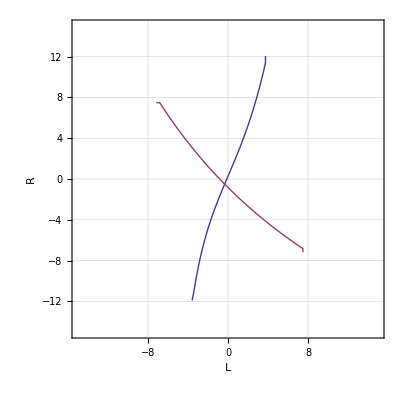

```mathematica
ParametricPlot[{
{Tavg[θNN ,0,1],Tavg[θNN ,0,2]},
{ΔT[θNN ,0,1],ΔT[θNN ,0,2]}
},
{θNN,40 °,140 °}
,AspectRatio->1,PlotRange->{{-15,15},{-15,15}},
GridLines->Automatic,GridLinesStyle->Directive[Dashed],
Frame->True,FrameLabel->{"L","R"}]
```

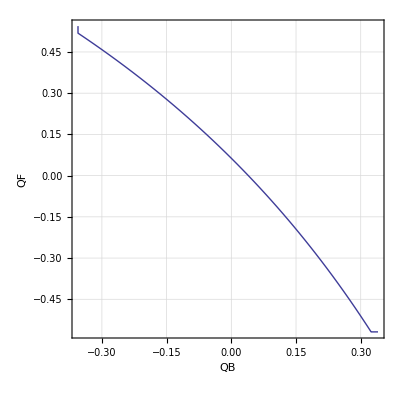

```mathematica
ParametricPlot[{
{Qlog[θNN ,0,1],Qlog[θNN ,0,2]}},
{θNN,40 °,140 °}
,AspectRatio->1,
GridLines->Automatic,GridLinesStyle->Directive[Dashed],
Frame->True,FrameLabel->{"QB","QF"}]
```

## Walk Effect

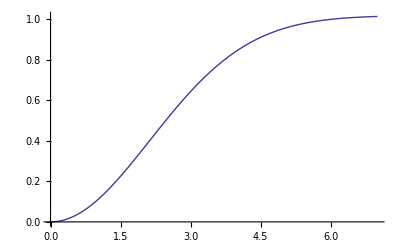

```mathematica
g[Q0_,t_]:=Q0(1-Exp[-(t/3)^2])/((1-Exp[-4])(* set g[6]==1 *))
Plot[g[1,t],{t,0,7},PlotRange->{All}]
```

```mathematica
gInv[Qth_,Q0_]:=3 √(-Log[1-Qth (1-Exp[-4])/Q0])
Manipulate[
Plot[gInv[Qth,Q0],{Q0,5,40}
,PlotRange->{{Qth,40},{0,6}},PlotLabel->"Qth="<>ToString[Qth]
,Frame->True, FrameLabel-> {"Q0","Trigger Time"}]
,{Qth,5,40}]
```

```mathematica
WalkB[θNN_,ϕNN_,id_,Qth_]:=gInv[Qth,QB[θNN,ϕNN,id]]
WalkF[θNN_,ϕNN_,id_,Qth_]:=gInv[Qth,QF[θNN,ϕNN,id]]
TB[θNN_,ϕNN_,id_,Qth_]:=ΓB[θNN,ϕNN,id]+gInv[Qth,QB[θNN,ϕNN,id]]
TF[θNN_,ϕNN_,id_,Qth_]:=ΓF[θNN,ϕNN,id]+gInv[Qth,QF[θNN,ϕNN,id]]
```

```mathematica
Manipulate[ParametricPlot[{
{TB[θNN °,0,1,Qth]-TF[θNN °,0,1,Qth],Qlog[θNN °,0,1]},
{TB[θNN °,0,2,Qth]-TF[θNN °,0,2,Qth],Qlog[θNN °,0,2]}
}
,{θNN , 40 , 140},PlotRange->All,AspectRatio->1]
,{Qth,0.01,4},{att,2000, 5000}]
```

```mathematica
Manipulate[ParametricPlot[{
{θ[P[θNN °,0,1]] 180/π,TB[θNN °,0,1,Qth]-TF[θNN °,0,1,Qth]+att/(βplastic c)Qlog[θNN °,0,1]},
{θ[P[θNN °,0,2]] 180/π,TB[θNN °,0,2,Qth]-TF[θNN °,0,2,Qth]+att/(βplastic c)Qlog[θNN °,0,2]}
}
,{θNN , 40 , 140},PlotRange->{{20,70},{-10,10}},AspectRatio->1]
,{Qth,0.01,4},{att,2000, 5000}]
```

```mathematica
Manipulate[ParametricPlot[{
{θ[P[θNN °,0,1]] 180/π,WalkB[θNN °,0,1,Qth]-WalkF[θNN °,0,1,Qth]},
{θ[P[θNN °,0,2]] 180/π,WalkB[θNN °,0,2,Qth]-WalkF[θNN °,0,2,Qth]}
}
,{θNN , 40 , 140},PlotRange->{{20,70},{-1,1}},AspectRatio->1]
,{Qth,0.01,4}]
```

```mathematica
ParametricPlot[
{
{ToF[P[θNN °,0,1],1],Qsum[θNN °,0,1]},
{ToF[P[θNN °,0,2],2],Qsum[θNN °,0,2]}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue}]
```

-Graphics-

```mathematica
ParametricPlot[
{
{ToF[P[θNN °,0,1],1],θ[P[θNN °,0,1]] 180/π},
{ToF[P[θNN °,0,2],2],θ[P[θNN °,0,2]] 180/π}
},
{θNN,40,140},PlotRange->All,GridLines->Automatic,GridLinesStyle->Directive[Dashed],
AspectRatio->1,PlotStyle->{Red,Blue}]
```

-Graphics-

```mathematica
Manipulate[
{{WalkB[θNN ,0,1,Qth],WalkF[θNN ,0,1,Qth]},
{TF[θNN ,0,1,Qth],QF[θNN ,0,1]},
{TB[θNN ,0,1,Qth],QB[θNN ,0,1]}
}
,{Qth,1,10},{θNN,40 °,140 °}]
```

```mathematica
Manipulate[
ParametricPlot[{
{ΓF[θNN ,0,1],QF[θNN ,0,1]},
{ΓB[θNN ,0,1],QB[θNN ,0,1]},
{(ΓF[θNN ,0,1]+ΓB[θNN ,0,1])/2,Qsum[θNN ,0,1]},
{TF[θNN ,0,1,Qth],QF[θNN ,0,1]},
{TB[θNN ,0,1,Qth],QB[θNN ,0,1]},
{(TF[θNN ,0,1,Qth]+TB[θNN ,0,1,Qth])/2,Qsum[θNN ,0,1]}
}
,{θNN,40 °,140 °}
,AspectRatio->1,PlotRange->{{10,30},{0,40}},PlotStyle->{Red, Blue, Black,Pink,Cyan,Gray },
GridLines->Automatic,GridLinesStyle->Directive[Dashed],
Frame->True,FrameLabel->{"TF","QF"}]
,{Qth,0.1,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{ΓB[θNN ,0,1]-ΓF[θNN ,0,1],Qsum[θNN ,0,1]},
{TB[θNN ,0,1,Qth]-TF[θNN ,0,1,Qth],Qsum[θNN ,0,1]},
{ΓB[θNN ,0,2]-ΓF[θNN ,0,2],Qsum[θNN ,0,2]},
{TB[θNN ,0,2,Qth]-TF[θNN ,0,2,Qth],Qsum[θNN ,0,2]}
}
,{θNN,40 °,140 °}
,AspectRatio->1,PlotRange->{{-10,10},{0,40}},PlotStyle->{Red, Blue, Black,Pink,Cyan,Gray },
GridLines->Automatic,GridLinesStyle->Directive[Dashed],
Frame->True,FrameLabel->{"TF","QF"}]
,{Qth,0.1,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{ΓB[θNN ,0,1]-ΓF[θNN ,0,1],ΓB[θNN ,0,2]-ΓF[θNN ,0,2]},
{TB[θNN ,0,1,Qth]-TF[θNN ,0,1,Qth],TB[θNN ,0,2,Qth]-TF[θNN ,0,2,Qth]}
}
,{θNN,40 °,140 °}
,AspectRatio->1,PlotRange->{{-10,10},{-10,10}},PlotStyle->{Red, Blue },
GridLines->{Table[i,{i,-10,10,1}],Table[i,{i,-10,10,1}]},GridLinesStyle->Directive[Gray],
Frame->True,FrameLabel->{"TF","QF"}]
,{Qth,0.1,4}]
```